Grafici della legge oraria e delle velocita` di 2 corpi che cadono dall’altezza di 11.03m con velocita` orizzontale rispettivamente nulla e pari a 5 m/s

Using a Table of parametric plots created with a range of the itime parameter {itime,0.0001,1.55,0.1}, such as it can be easily transformed later into an animated gif. Note that the time cannot start from 0.

11.0363

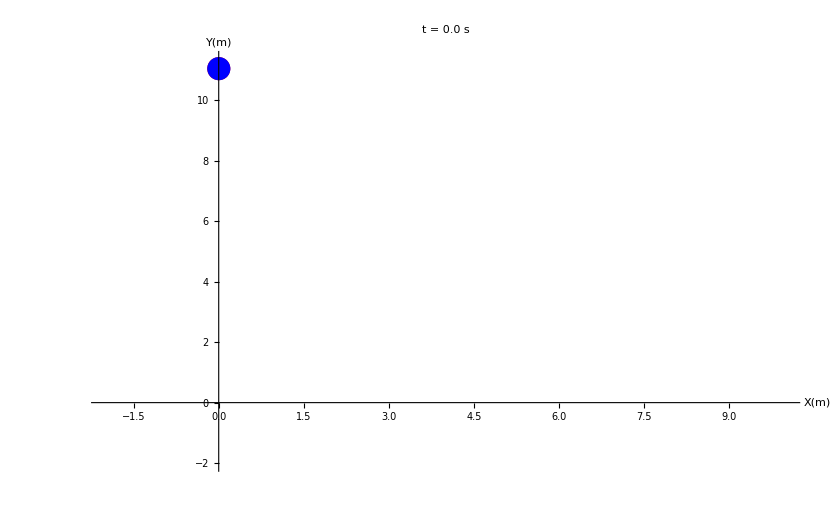
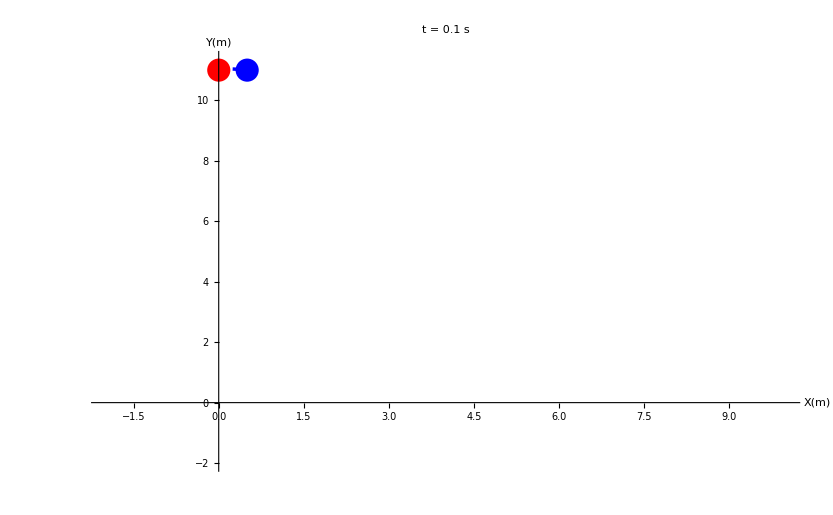
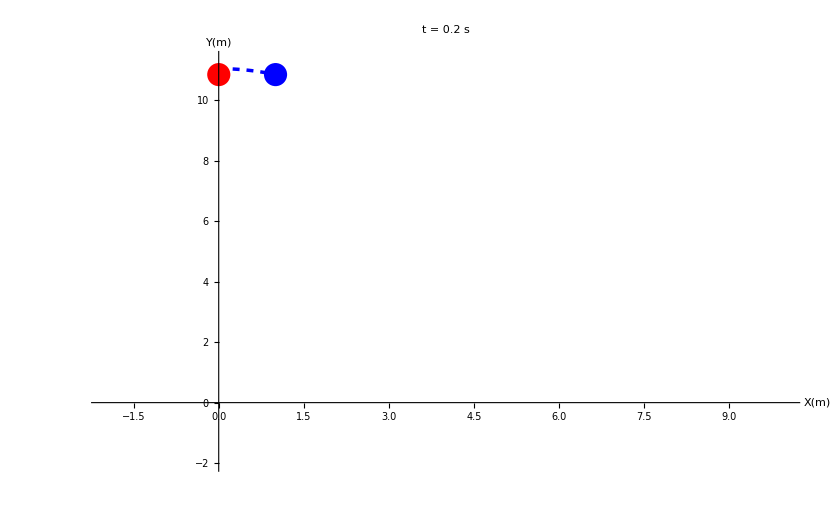
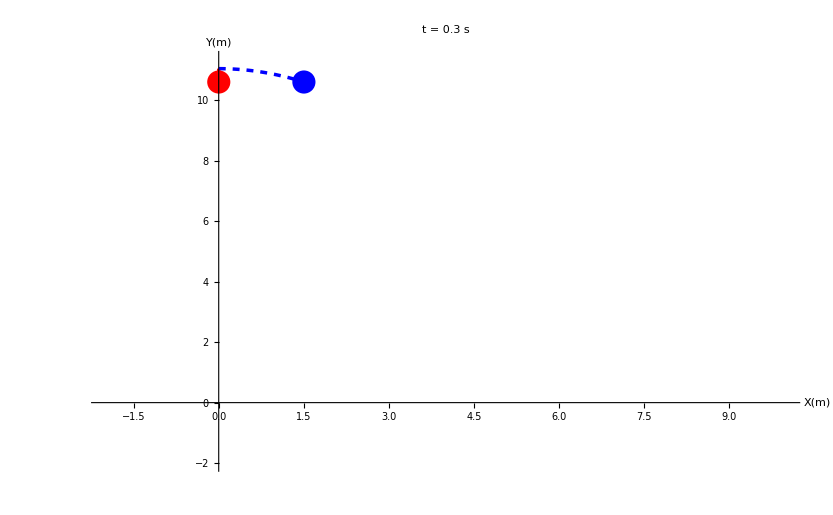
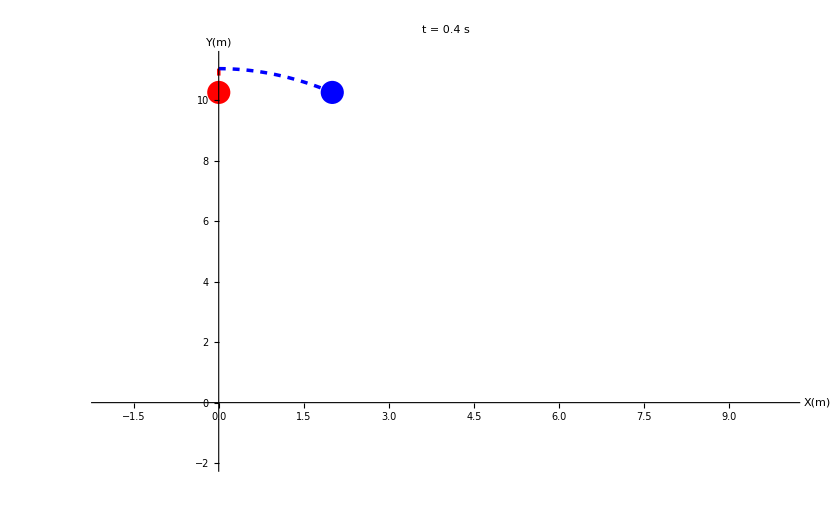
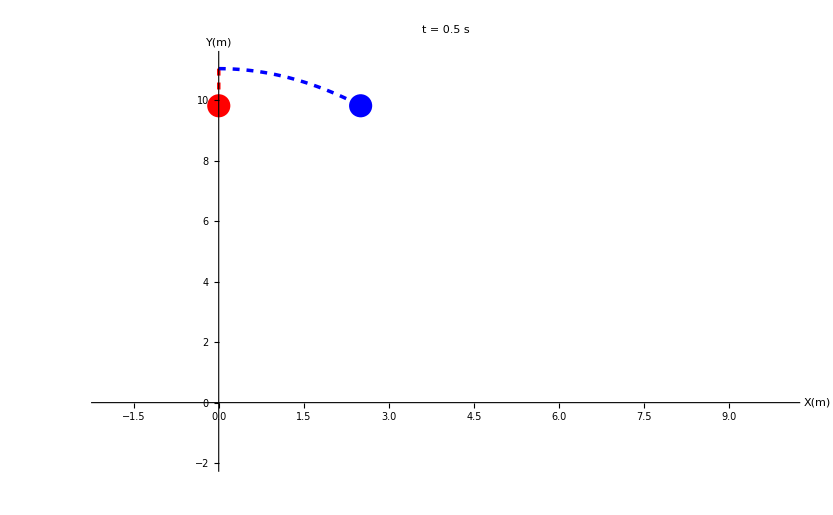
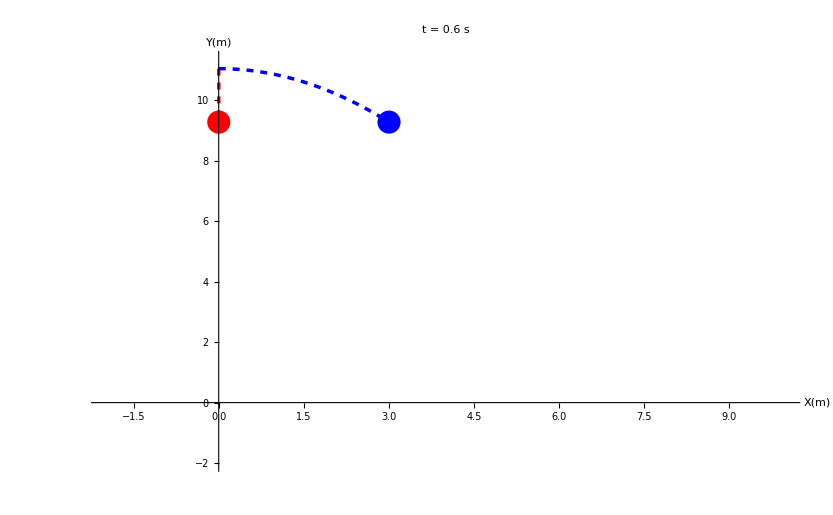
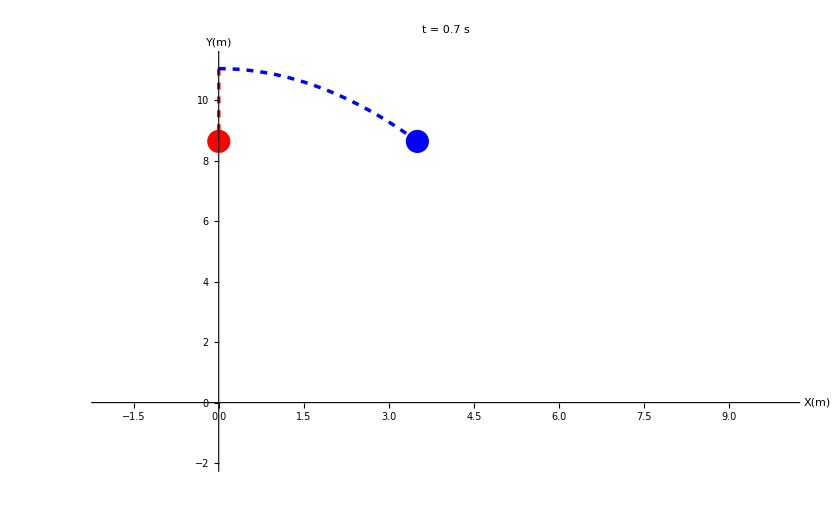

```mathematica
H=0.5* 9.81*1.5^2
plots=Table[ParametricPlot[{{0.001,H-0.5*9.81*t^2},{0.001+5*t,H-0.5*9.81*t^2}},{t,0,itime},PlotRange->{{-2,10},{-2,H+0.3}},AxesLabel->{X [m],Y[m]}, BaseStyle->{FontWeight->"Bold",FontSize->18}, LabelStyle-> Directive[Blue,Bold],PlotLabel->"t = "<>ToString[NumberForm[itime,{2,1}]]<> " s",ImageSize->{833,515},AspectRatio->Full,PlotStyle->{{Red,Thick, Dashed,Thickness[0.003]},{Blue,Thick,Dashed,Thickness[0.003]}},Epilog->{{Red,PointSize[0.02],Point[{0.001,H-0.5*9.81*itime^2}]},{Blue,PointSize[0.02],Point[{0.001+5*itime,H-0.5*9.81*itime^2}]}}],
{itime,0.0001,1.55,0.1}]
```

```mathematica
SetDirectory@NotebookDirectory[]
Export["animation.gif",plots,"DisplayDurations"->0.5]
```

/Users/meridian/scratch/Mathematica/FallingObjects

animation.gif

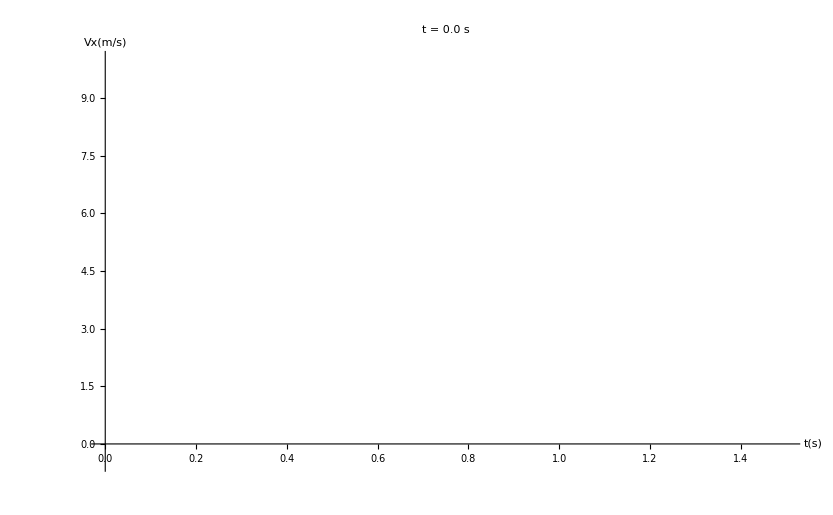
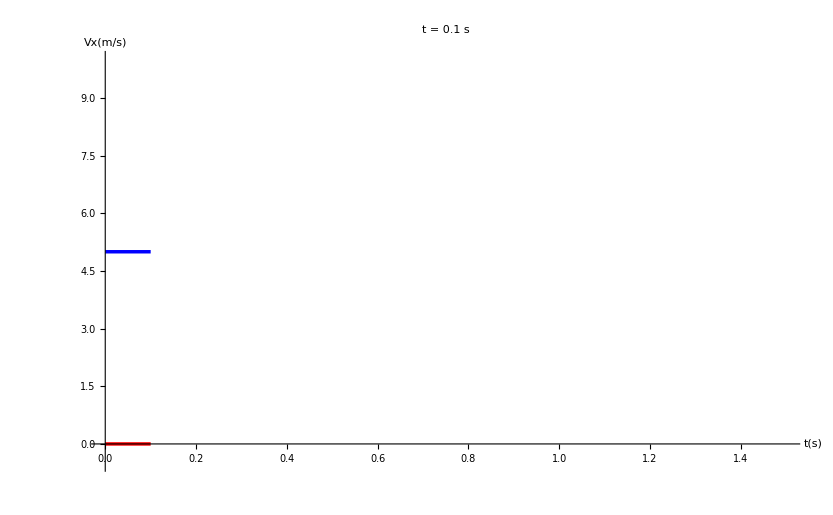
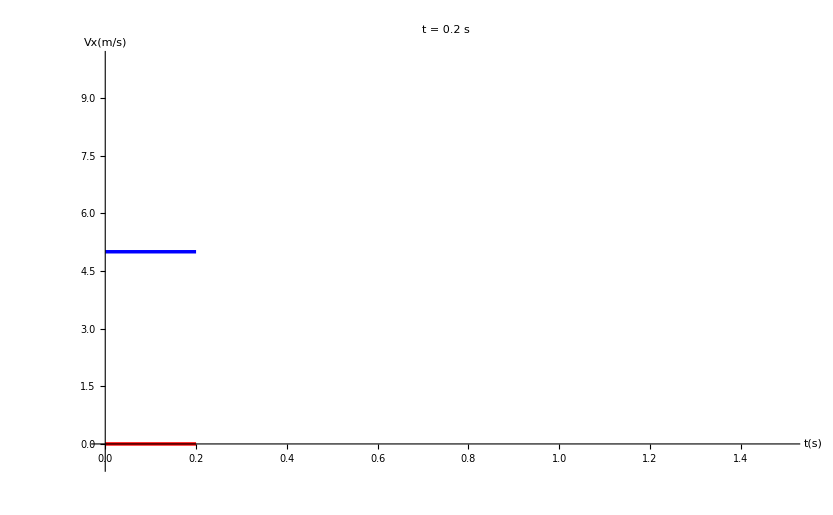
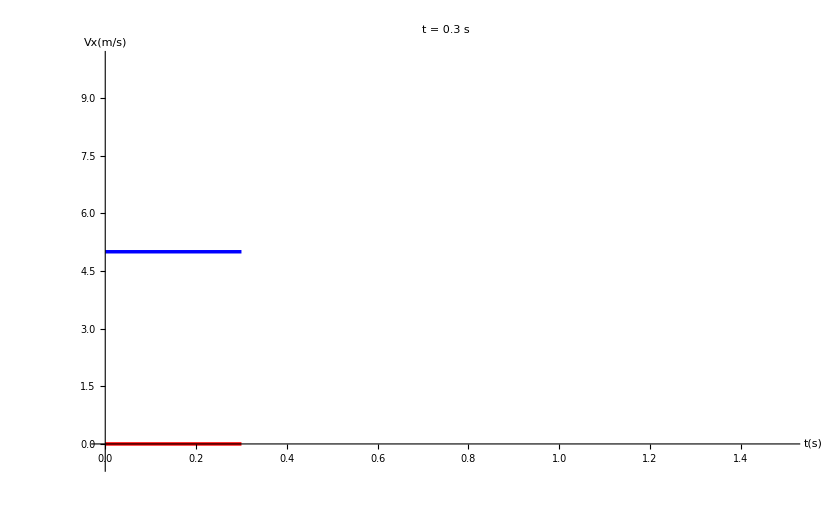
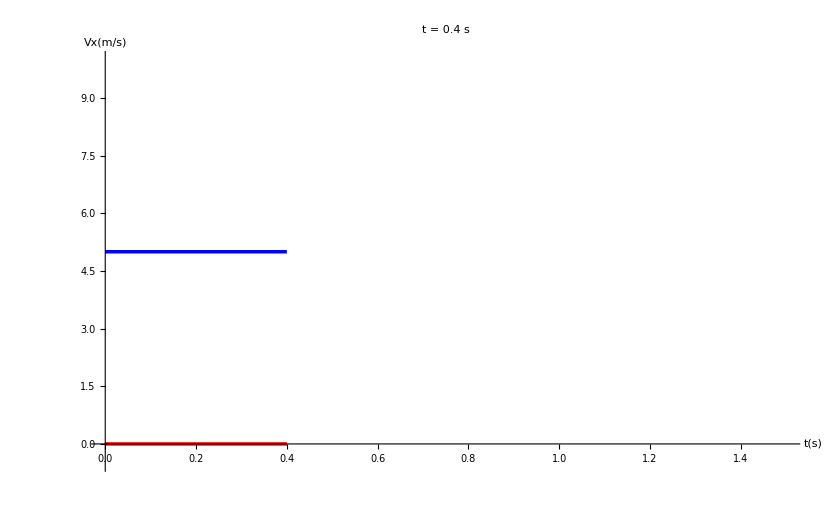
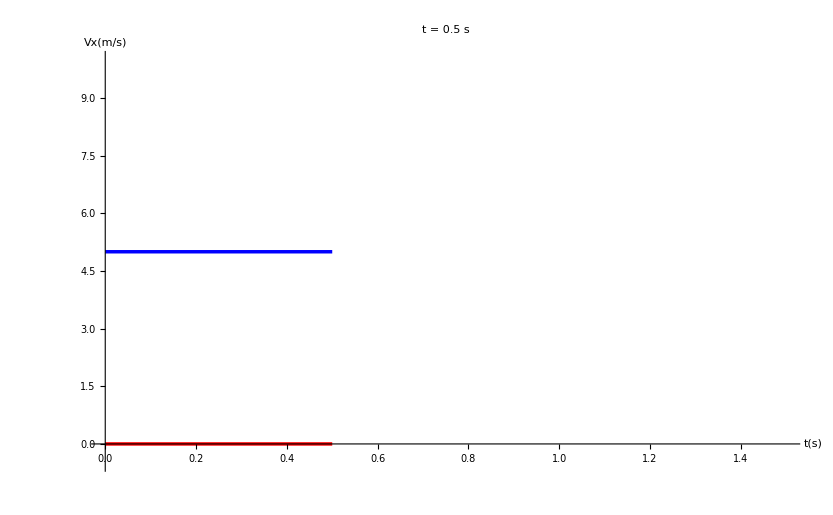
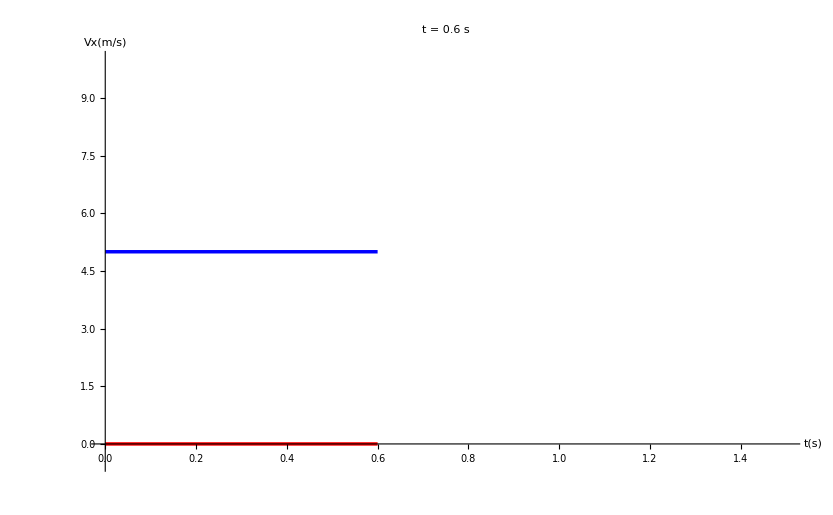
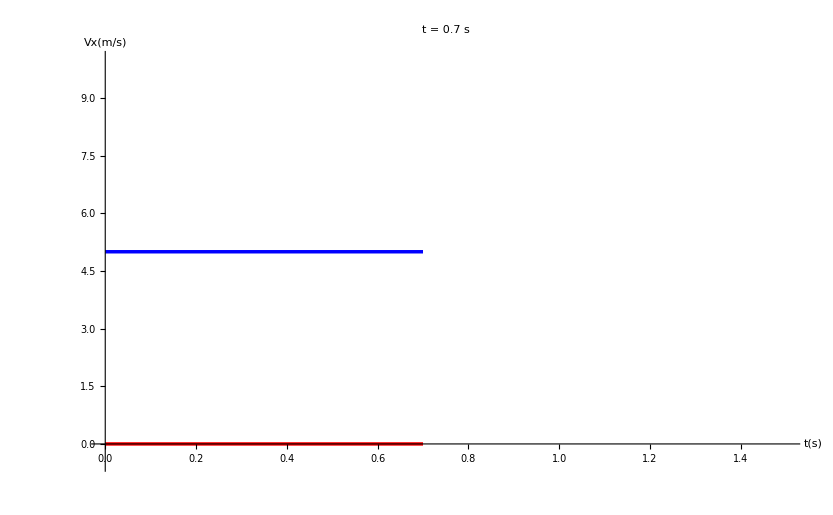

```mathematica
plotsvx=Table[Plot[ {0,5},{t,0,itime},PlotRange->{{0,1.5},{-0.5,10.}},AxesLabel->{"t(s)","Vx(m/s)"}, BaseStyle->{FontWeight->"Bold",FontSize->18}, LabelStyle-> Directive[Blue,Bold],PlotLabel->"t = "<>ToString[NumberForm[itime,{2,1}]]<> " s",ImageSize->{833,515},AspectRatio->Full,PlotStyle->{{Red,Dashing[none],Thickness[0.003]},{Blue,Dashing[none],Thickness[0.003]}}],
{itime,0.0001,1.55,0.1}]
plotsvy=Table[Plot[ {9.81*t,9.81*t},{t,0,itime},PlotRange->{{0,1.5},{-0.5,20.}},AxesLabel->{"t(s)","Vy(m/s)"}, BaseStyle->{FontWeight->"Bold",FontSize->18}, LabelStyle-> Directive[Blue,Bold],PlotLabel->"t = "<>ToString[NumberForm[itime,{2,1}]]<> " s",ImageSize->{833,515},AspectRatio->Full,PlotStyle->{{Red,Dashing[none],Thickness[0.003]},{Blue,Dashing[none],Thickness[0.003]}}],
{itime,0.0001,1.55,0.1}]
```

```mathematica
SetDirectory@NotebookDirectory[]
Export["animation_vx.gif",plotsvx,"DisplayDurations"->0.5]
Export["animation_vy.gif",plotsvy,"DisplayDurations"->0.5]
```

/Users/meridian/scratch/Mathematica/FallingObjects

animation_vx.gif

animation_vy.gif

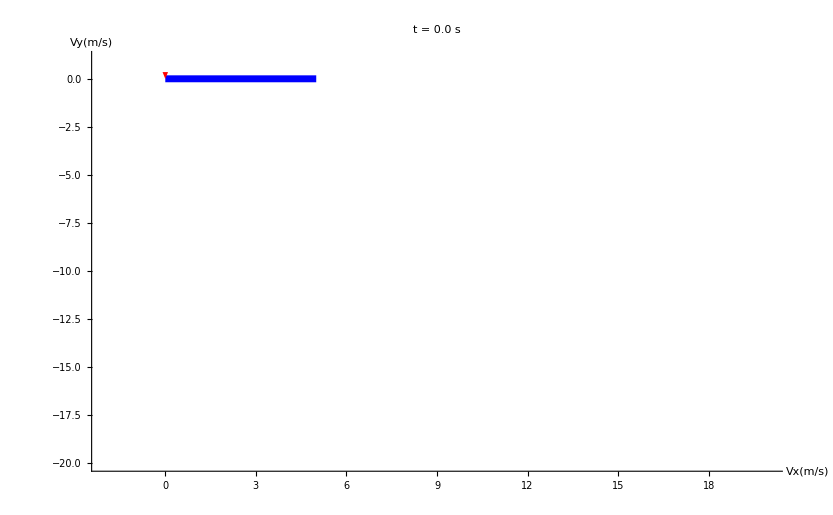
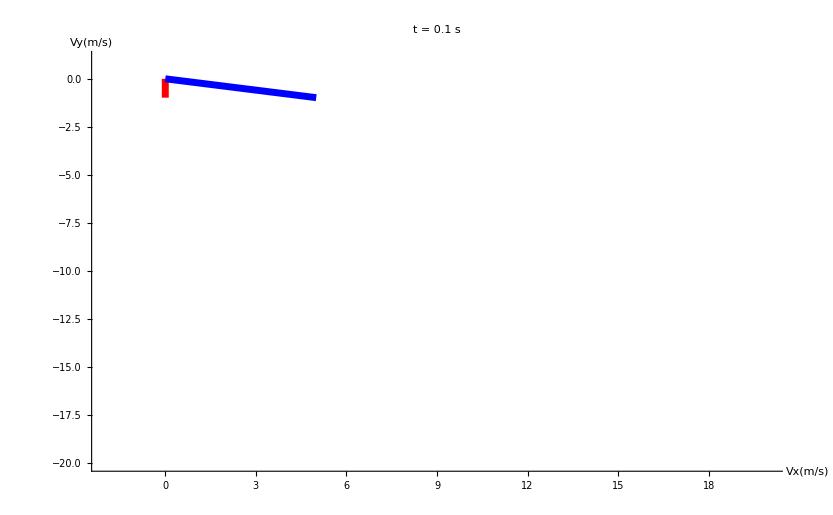
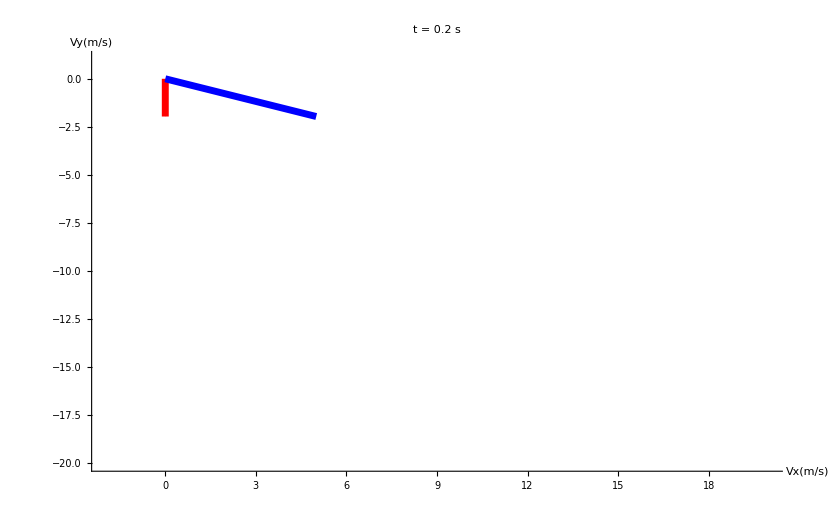
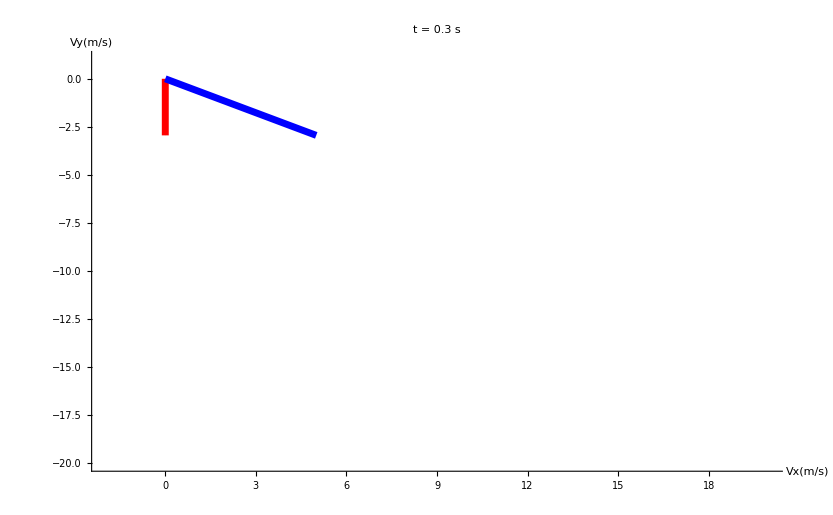
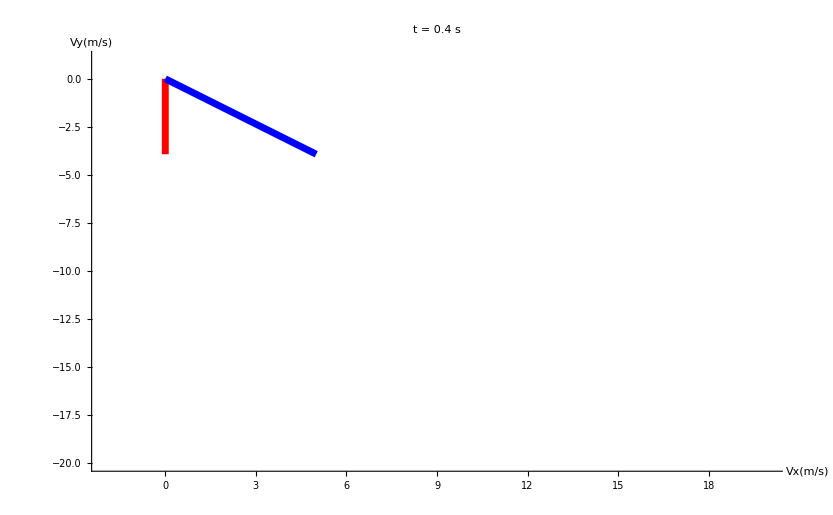
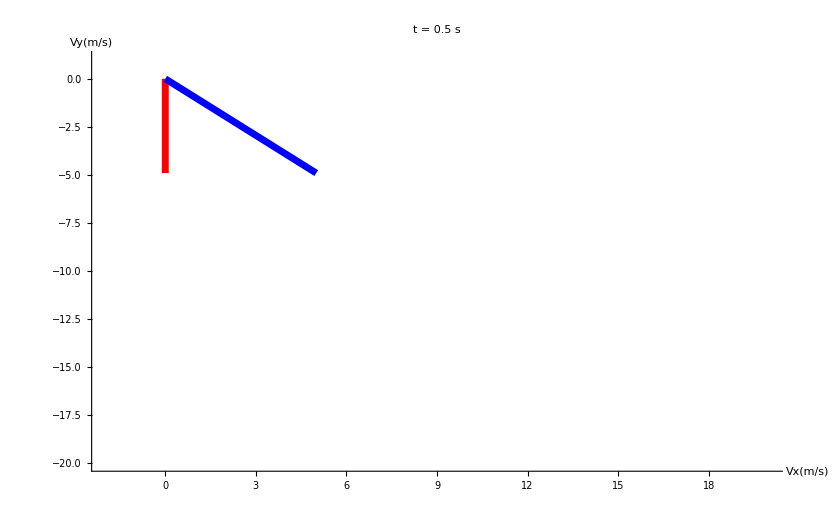
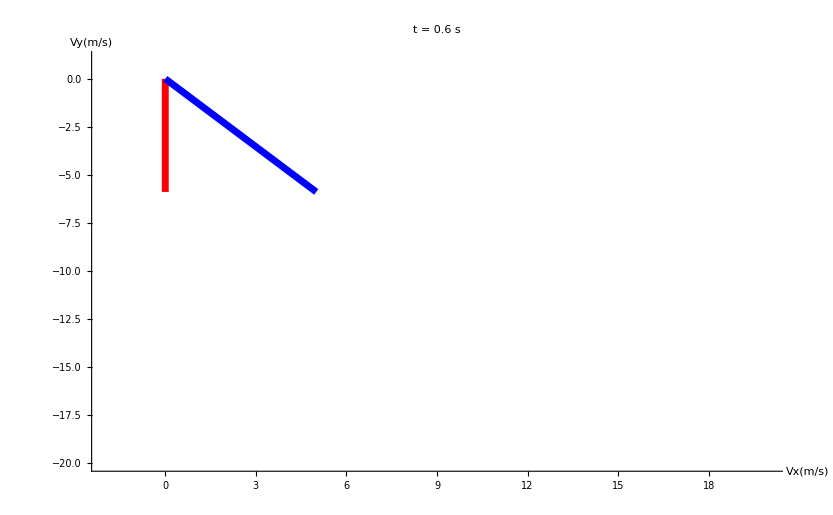
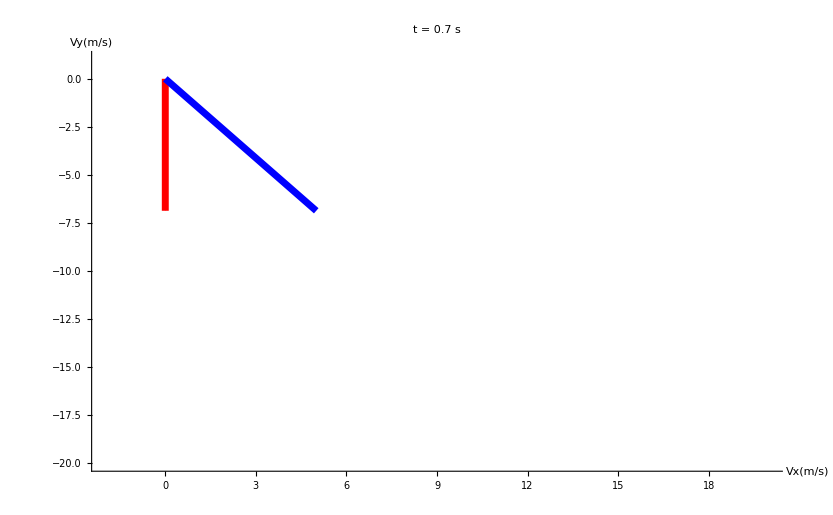

```mathematica
plotsv=Table[Graphics[{Arrowheads[.028],Thickness[0.006],{Red,Arrow[{{0,0},{0,-9.81*itime}}]},{Blue,Arrow[{{0,0},{5.,-9.81*itime}}]}},PlotRange->{{-2.,20.},{-20,1}},Axes->True,AxesLabel->{"Vx(m/s)","Vy(m/s)"}, BaseStyle->{FontWeight->"Bold",FontSize->18},LabelStyle-> Directive[Blue,Bold],ImageSize->{833,515},AspectRatio->Full,PlotLabel->"t = "<>ToString[NumberForm[itime,{2,1}]]<> " s"],{itime,0.0001,1.55,0.1}]
```

```mathematica
SetDirectory@NotebookDirectory[]
Export["animation_v.gif",plotsv,"DisplayDurations"->0.5]
```

/Users/meridian/scratch/Mathematica/FallingObjects

animation_v.gif

Now try to measure the space for the object with initial speed

```mathematica
v[t_?NumericQ]=Sqrt[5^2+9.81^2*t^2]
```

√(25+96.2361 t^2)

```mathematica
s[t_?NumericQ]=Integrate[v[x],{x,0,t}]
```

∫_0^t v[x]ⅆx

```mathematica
Table[ "t= " <> ToString [t] <> " rel diff in space = " <> ToString[N[(s[t]-0.5*9.81*t^2)/s[t],4]] <>"\n",{t,1,10.,1.}]
```

{t= 1. rel diff in space = 0.330196
,t= 2. rel diff in space = 0.14295
,t= 3. rel diff in space = 0.0789409
,t= 4. rel diff in space = 0.050202
,t= 5. rel diff in space = 0.0348782
,t= 6. rel diff in space = 0.0257296
,t= 7. rel diff in space = 0.0198179
,t= 8. rel diff in space = 0.0157686
,t= 9. rel diff in space = 0.0128684
,t= 10. rel diff in space = 0.0107167
}

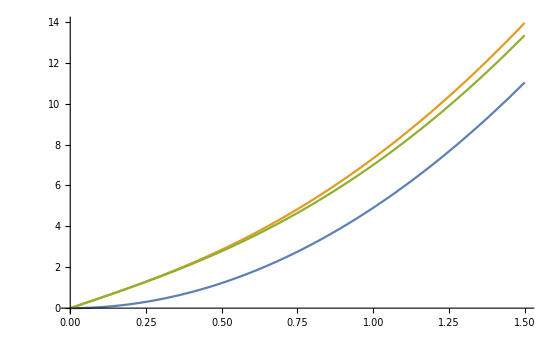

```mathematica
Plot[{0.5*9.81*t^2,s[t],Sqrt[25*t^2+(0.5*9.81*t^2)^2]},{t,0,1.5}]
```